In this nb we reproduce some of the results published in "Excitation of scalar quasi-normal modes from boson clouds", arXiv : 2512.15878 by Cannizzaro et al. 
We first introduce QNMs and QBSs of massive scalar field, show their orthogonality with respect to the bilinear form, and finally compute their mutual excitation in the presence of an external tidal potential . While this nb focuses on the case α = 0.3, the spectrum of other masses is reported in the last section . For questions or comments, send an email to enrico.cannizzaro@tecnico.ulisboa.pt.

Note: Figs 8 and 9 were based on the private code of Ref. arXvi: 2305.15460 (JCAP 07 (2023) 070), and are not included in this notebook.

```mathematica
Quit[]
```

## Orthogonality

### Modes

#### Mode solver

```mathematica
INT[w_,mu_,ar_,l_,m_,s_,NITMAX_, sign_]:=(
M=1;
br=Sqrt[1-ar^2];
rminus=(1-br);
rplus=1+br;
k1=1/2*Abs[m-s];
k2=1/2*Abs[m+s];
OmegaH=ar/(2*M*rplus);
(******)
(*η=Max[Abs[m],Abs[s]];
α=η+m s/η;β=η-m s/η;
gino1=z^2-1/4(α+β)^2;gino2=z^2-1/4(α-β)^2;
h=(gino1(z^2-s^2) gino2)/(2(z-1/2)z^3(z+1/2));
f0=l(l+1)-s(s+1);f1=-2 m s^2/(l(l+1));f2=(h/.z->(l+1))-(h/.z->l)-1;
Alm=f0+f1 Sqrt[ar^2 (w^2-mu^2)]*0+ f2*ar^2 (w^2-mu^2);*)
(******)

(******)
Alm=SpheroidalEigenvalue[l,m,I ar √(w^2-mu^2)]-ar^2 (w^2-mu^2);

Clear[α,β,γ];
q=sign*Sqrt[mu^2-w^2];
c0=1-2*I*w-2*I/br*(w-ar*m/2);
c1=-4+4*I*(w-I*q*(1+br))+4*I/br*(w-ar*m/2)-2*(w^2+q^2)/q;
c2=3-2*I*w-2*I/br*(w-ar*m/2)-2*(q^2-w^2)/q;c3=2*I*(w-I*q)^3/q+2*(w-I*q)^2*br+q^2*ar^2+2*I*q*ar*m-Alm-1-(w-I*q)^2/q+2*q*br+2*I/br*((w-I*q)^2/q+1)*(w-ar*m/2);c4=(w-I*q)^4/q^2+2*I*w*(w-I*q)^2/q-2*I/br*(w-I*q)^2/q*(w-ar*m/2);γ=Function[n,n^2+(c2-3)*n+c4+(-c2+2)*0];
β=Function[n,-2*n^2+(c1+2)*n+c3];
α=Function[n,n^2+(c0+1)*n+c0];

Leaver31=Module[{Rn},For[{n=NITMAX;Rn=-1.0;},n>0,{Rn=γ[n]/(β[n]-α[n]*Rn);n--;}
];Rn];

β[0]/α[0]-Leaver31
)
```

```mathematica
INT[(*w*)0.29-0.09*I,(*mu*)0.2,(*ar*)0.5,(*l*)1,(*m*)1,(*s*)0,(*NITMAX*)500, -1]
```

-1.53526-2.50005 ⅈ

```mathematica
ωQBS[n_, l_, m_]:= mu0(1-mu0^2/(2 n^2)-(1/(8n)+6/(2l+1)-2/n)mu0^4/n^3);
```

#### fundamental QBS 0.3

```mathematica
(*CHOOSE SIGN=-1 FOR QBS AND 1 FOR QNM*)
```

```mathematica
mu0=0.3;
a0=0.0;
l0=1;
m0=1;
N0=1000;
wguess=ωQBS[2,1,1];

f[x_?NumberQ]:=INT[x,mu0,a0,l0,m0,0,N0, -1];
root=x/.FindRoot[f[x],{x,wguess}];
check=Abs[f[root]];
{root,check}
```

{0.296192-9.45565×10^-6 ⅈ,5.44179×10^-15}

```mathematica
ωn1=0.2961923463989993-9.455651669997343*^-6 ⅈ;
```

#### Wavefunction fundamental QBS 0.3

```mathematica
ae[0]=1;
ae[1]=-β[0]/α[0]/.w->root;
i=1;While[i<N0,ae[i+1]=(-β[i]*ae[i]-γ[i]*ae[i-1])/(α[i])/.w->root;i=i+1];
```

```mathematica
chi=(mu0^2-2*w^2)/q/.w->root;
sigma=2*rplus*(w-m0*a0/(2*M*rplus))/(rplus-rminus)/.w->root;
Rpsi=(Exp[I Pi/2](r-rplus))^(-I*sigma)Exp[(-I Pi/2)(-I sigma)]*(r-rminus)^(I*sigma+chi-1)*Exp[q*r]*Sum[ae[n]*(r-rplus)^n/(r-rminus)^n,{n,0,N0}];
```

```mathematica
Rn1=Rpsi*r;
```

#### fundamental QNM 0.3

```mathematica
mu0=0.3;
a0=0.0;
l0=1;
m0=1;
N0=1000;
wguess=0.310957- 0.086593 I;

f[x_?NumberQ]:=INT[x,mu0,a0,l0,m0,0,N0, 1];
root=x/.FindRoot[f[x],{x,wguess}];
check=Abs[f[root]];
{root,check}
```

{0.333777-0.0716577 ⅈ,8.67112×10^-16}

```mathematica
ωnQNM=0.33377719374400316-0.07165770987980352 ⅈ;
```

#### Wavefunction fundamental QNM 0.3

```mathematica
ae[0]=1;
ae[1]=-β[0]/α[0]/.w->root;
i=1;While[i<N0,ae[i+1]=(-β[i]*ae[i]-γ[i]*ae[i-1])/(α[i])/.w->root;i=i+1];
```

```mathematica
chi=(mu0^2-2*w^2)/q/.w->root;
sigma=2*rplus*(w-m0*a0/(2*M*rplus))/(rplus-rminus)/.w->root;
RpsiQNM=(Exp[I Pi/2](r-rplus))^(-I*sigma)Exp[(-I Pi/2)(-I sigma)]*(r-rminus)^(I*sigma+chi-1)*Exp[q*r]*Sum[ae[n]*(r-rplus)^n/(r-rminus)^n,{n,0,N0}];
```

```mathematica
Rn1QNM=RpsiQNM*r;
```

### QNM-QBS orthogonality product

#### Product

```mathematica
Integrand=(1-(2M)/r)^-1 Rn1QNM*Rn1//.r-> (re + I im)
```

```mathematica
Integrand//.re-> 2.1//.im-> 300
```

General::munfl: 1/(2.1+300. ⅈ)^251 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/(2.1+300. ⅈ)^250 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/(2.1+300. ⅈ)^249 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

3.16141×10^-20+3.33274×10^-20 ⅈ

```mathematica
Integrandfirstpath=Integrand//.re-> 1.9;
Integrandsecondpath=Integrand//.im-> -1;
Integrandthirdpath=Integrand//.re-> 2.1;
```

```mathematica
function[regul_]:=NIntegrate[Rationalize[I*Integrandfirstpath,0],{im,regul,-1},AccuracyGoal->40,(*PrecisionGoal->8,*) Method->"LocalAdaptive"]+ NIntegrate[Rationalize[Integrandsecondpath,0],{re,1.9,2.1},AccuracyGoal->40,(*PrecisionGoal->8,*) Method->"LocalAdaptive"]+NIntegrate[Rationalize[I*Integrandthirdpath,0],{im,-1, regul},AccuracyGoal->40,(*PrecisionGoal->8,*) Method->"LocalAdaptive"]
```

```mathematica
OVERLAP=Monitor[Table[{i,function[i]},{i,30,90,5}],i]
```

{{30,7.47125+9.41795 ⅈ},{35,1.03475+6.06697 ⅈ},{40,-0.973148+2.90177 ⅈ},{45,-1.07605+1.02722 ⅈ},{50,-0.681594+0.198439 ⅈ},{55,-0.327608-0.0631376 ⅈ},{60,-0.122343-0.0948936 ⅈ},{65,-0.0306326-0.0641323 ⅈ},{70,0.000540124-0.0323171 ⅈ},{75,0.00668332-0.0129598 ⅈ},{80,0.00524725-0.00388919 ⅈ},{85,0.00285835-0.000529431 ⅈ},{90,0.00124026+0.000342718 ⅈ}}

```mathematica
OVERLAPABS=OVERLAP//Abs;
```

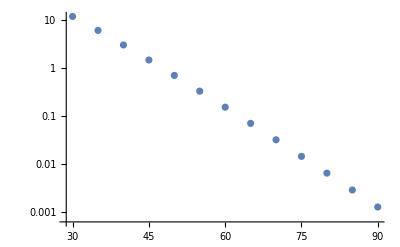

```mathematica
ListLogPlot[OVERLAPABS,PlotRange->All]
```

```mathematica
(*THE INTEGRAL CONVERGES TO ZERO WITH INCREASING Im(r_infty): THE MODES ARE ORTHOGONAL*)
```

### QNM-QBS normalizations

```mathematica
(*here we compute the normalization factor for the modes. for QBS, we will use the boundary-term regularization of the bilinear form  presented in 2309.10021*)
```

#### normalization factor for QBS

```mathematica
OverlapInterpBoundaryofM[yp_,ye_,ωp_,ωe_,regul_,rinf_, M_?NumericQ]:=NIntegrate[Rationalize[(1-(2M)/r)^-1(ye)(yp) ,0],{r,2M(1+regul),10000},AccuracyGoal->30,(*PrecisionGoal->8,*) Method->"LocalAdaptive"]+Rationalize[ⅈ/(ωp+ωe)(ye/.r-> (2M(1+regul)))(yp/.r-> (2M(1+regul))) ,0]
```

```mathematica
test=Monitor[Table[{eps,
OverlapInterpBoundaryofM[Rn1,Rn1,ωn1,ωn1,eps,1000, 1]//Abs},{eps,0.01,0.1,0.01}],eps//N];
```

General::munfl: 0.02^1000 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.02^999 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.02^998 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

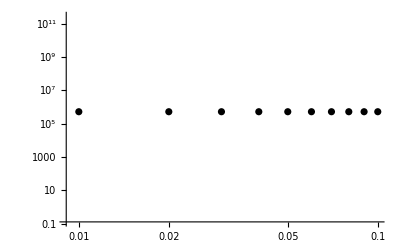

```mathematica
Show[ListLogLogPlot[{test⟦1;;-1⟧},PlotRange->All,PlotStyle->{Black,Dashed}]
]
```

```mathematica
test
```

{{0.01,525229.},{0.02,525230.},{0.03,525230.},{0.04,525231.},{0.05,525231.},{0.06,525231.},{0.07,525231.},{0.08,525231.},{0.09,525231.},{0.1,525230.}}

```mathematica
(*converges with epsilon. we extract the normalization value*)
```

```mathematica
NormQBS=525229.5048409974;
```

#### normalization factor for QNM

```mathematica
IntegrandQNMnorm=(1-(2M)/r)^-1 Rn1QNM*Rn1QNM//.r-> (re + I im)
```

```mathematica
IntegrandQNMnormfirstpath=IntegrandQNMnorm//.re-> 1.9;
```

```mathematica
IntegrandQNMnormsecondpath=IntegrandQNMnorm//.im-> -1;
```

```mathematica
IntegrandQNMnormthirdpath=IntegrandQNMnorm//.re-> 2.1;
```

```mathematica
functionQNM[regul_]:=NIntegrate[Rationalize[IntegrandQNMnormfirstpath,0],{im,regul,-1},AccuracyGoal->30,(*PrecisionGoal->8,*) Method->"LocalAdaptive"]+ NIntegrate[Rationalize[IntegrandQNMnormsecondpath,0],{re,1.9,2.1},AccuracyGoal->30,(*PrecisionGoal->8,*) Method->"LocalAdaptive"]+NIntegrate[Rationalize[IntegrandQNMnormthirdpath,0],{im,-1, regul},AccuracyGoal->30,(*PrecisionGoal->8,*) Method->"LocalAdaptive"]
```

```mathematica
tableQNM=Monitor[Table[{i,functionQNM[i]},{i,12,35,2}],i]
```

{{12,-34.826-10.7778 ⅈ},{14,-34.8021-10.7528 ⅈ},{16,-34.8009-10.7367 ⅈ},{18,-34.8052-10.7305 ⅈ},{20,-34.8086-10.7294 ⅈ},{22,-34.8102-10.7299 ⅈ},{24,-34.8106-10.7306 ⅈ},{26,-34.8106-10.731 ⅈ},{28,-34.8105-10.7311 ⅈ},{30,-34.8104-10.7311 ⅈ},{32,-34.8104-10.7311 ⅈ},{34,-34.8104-10.7311 ⅈ}}

```mathematica
tableQNMabs=tableQNM//Abs
```

{{12,36.4556},{14,36.4253},{16,36.4195},{18,36.4217},{20,36.4247},{22,36.4263},{24,36.427},{26,36.4271},{28,36.427},{30,36.4269},{32,36.4269},{34,36.4269}}

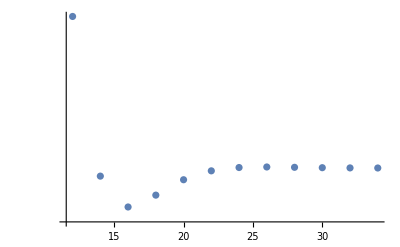

```mathematica
ListLogPlot[tableQNMabs,PlotRange->All]
```

```mathematica
(*converges with high Im(Subscript[r, infty]). We extract the norm*)
```

```mathematica
NormQNM=36.42687526245358;
```

```mathematica
normalizationfactor=√(NormQBS*NormQNM)
```

4374.07

#### Fig 2

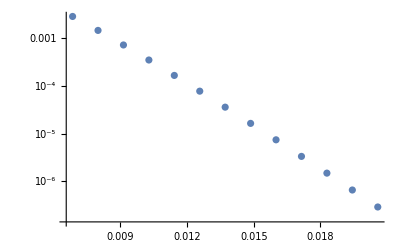

```mathematica
ListLogPlot[OVERLAPABS/normalizationfactor,PlotRange->All]
```

## TIDAL POTENTIAL

### QNM-QBS excitation through tidal potential

```mathematica
(*we study the overlap with tidal potentials. We adopt a smoothening procedure as detailed in the paper*)
```

#### Potential

```mathematica
Fapprox[r_, R_, l_]:= r^l/(R^(l+1)(1+(r/R)^(2l+1)));
F[r_, R_, l_]:= r^l/R^(l+1)HeavisideTheta[R-r]+R^l/r^(l+1)HeavisideTheta[r-R];
```

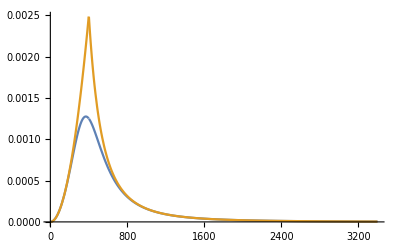

```mathematica
Plot[{Fapprox[r, 400, 2], F[r, 400, 2]},{r, 2,3400}, PlotRange->All]
```

```mathematica
Series[ r^l/(R^(l+1)(1+(r/R)^(2l+1)))//.l-> 2, {R, Infinity, 4}]
```

r^2/R^3+O[1/R]^5

```mathematica
Clear[IntegrandTidal, Integrandfirstpath, Integrandsecondpath, Integrandthirdpath]
```

```mathematica
IntegrandTidal[re_,im_, R_,l_]:=(1-(2M)/r)^-1 r^l/(R^(l+1)(1+(r/R)^(2l+1))) Rn1QNM*Rn1//.r-> (re + I im)
```

#### complex integral: first term

```mathematica
Integrandfirstpath[im_, R_,l_]:=IntegrandTidal[1.9, im, R,l]
```

#### complex integral: second term

```mathematica
Integrandsecondpath[re_, R_,l_]:=IntegrandTidal[re, -1, R,l]
```

#### complex integral: third term

```mathematica
Integrandthirdpath[im_, R_,l_]:=IntegrandTidal[2.1, im, R,l]
```

#### QBS-V-QNM matrix element

```mathematica
function[regul_, R_, l_]:=NIntegrate[Rationalize[I*Integrandfirstpath[im, R, l],0],{im,regul,-1},AccuracyGoal->30,(*PrecisionGoal->8,*) Method->"LocalAdaptive"]+ NIntegrate[Rationalize[Integrandsecondpath[re, R, l],0],{re,1.9,2.1},AccuracyGoal->30,(*PrecisionGoal->8,*) Method->"LocalAdaptive"]+NIntegrate[Rationalize[I*Integrandthirdpath[im, R, l],0],{im,-1, regul},AccuracyGoal->30,(*PrecisionGoal->8,*) Method->"LocalAdaptive"]
```

```mathematica
function[30, 40, 2]
```

0.134478-0.460828 ⅈ

```mathematica
over=Monitor[Table[{i,function[i, 40, 2]},{i,30,110,10}],i]
```

{{30,0.134478-0.460828 ⅈ},{40,0.291929-0.432073 ⅈ},{50,0.321681-0.405157 ⅈ},{60,0.322765-0.399052 ⅈ},{70,0.32226-0.398372 ⅈ},{80,0.322145-0.398366 ⅈ},{90,0.322134-0.398377 ⅈ},{100,0.322135-0.39838 ⅈ},{110,0.322135-0.39838 ⅈ}}

```mathematica
overabs=over//Abs
```

{{30,0.480048},{40,0.52145},{50,0.51733},{60,0.513244},{70,0.512398},{80,0.512321},{90,0.512323},{100,0.512325},{110,0.512326}}

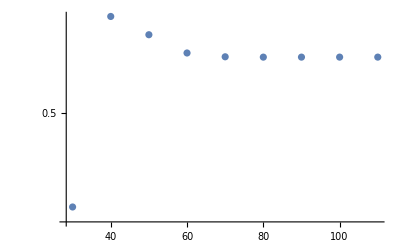

```mathematica
ListLogPlot[overabs,PlotRange->All]
```

```mathematica
matrixelementQBSQNM=overabs⟦-1,2⟧/normalizationfactor
```

0.000117128

#### comparison with QBS-V-QBS matrix element

```mathematica
(*let us compare this result with the <QBS|V|QBS> case*)
```

```mathematica
OverlapInterpBoundaryofM[yp_,ye_,ωp_,ωe_,regul_,rinf_,l_, R_,  M_?NumericQ]:=NIntegrate[Rationalize[(1-(2M)/r)^-1 r^l/(R^(l+1)(1+(r/R)^(2l+1)))(ye)(yp) ,0],{r,2M(1+regul),10000},AccuracyGoal->30,(*PrecisionGoal->8,*) Method->"LocalAdaptive"](*+Rationalize[ⅈ/(ωp+ωe)(ye/.r-> (2M(1+regul)))(yp/.r-> (2M(1+regul))) ,0]*)
```

```mathematica
test=Monitor[Table[{eps,
OverlapInterpBoundaryofM[Rn1,Rn1,ωn1,ωn1,eps,1000,2, 40, 1]//Abs},{eps,0.01,0.05,0.01}],eps//N];
```

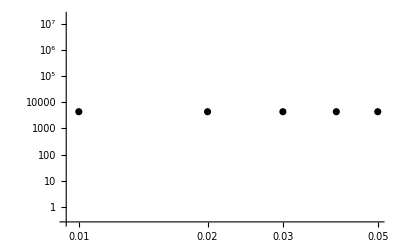

```mathematica
Show[ListLogLogPlot[{test⟦1;;-1⟧},PlotRange->All,PlotStyle->{Black,Dashed}]
]
```

```mathematica
test
```

{{0.01,4322.96},{0.02,4322.96},{0.03,4322.96},{0.04,4322.96},{0.05,4322.96}}

```mathematica
matrixelementQBSQBS=test⟦-1,2⟧/NormQBS
matrixelementQBSQBS/matrixelementQBSQNM
```

0.00823062

0.0160652

```mathematica
(*the QBS-QBS is a few orders of magnitude higher then the QBS-QNM one*)
```

#### QBS-V-QNM matrix element as a function of R (Fig 7)

```mathematica
varyingR=Monitor[Table[{i,function[110,i, 2]/normalizationfactor//Abs},{i,6,120,12}],i];
```

```mathematica
varyingRQBS=Monitor[Table[{R,
OverlapInterpBoundaryofM[Rn1,Rn1,ωn1,ωn1,2/100,1000,2, R, 1]/NormQBS//Abs},{R,6,120,12}],R//N];
```

```mathematica
Beep[]
```

```mathematica
ratio=Table[Null, Length[varyingR]];
```

```mathematica
Do[ratio[[i]]={varyingR[[i]][[1]], varyingR[[i]][[2]]/varyingRQBS[[i]][[2]]},{i, 1, Length[varyingR]}]
```

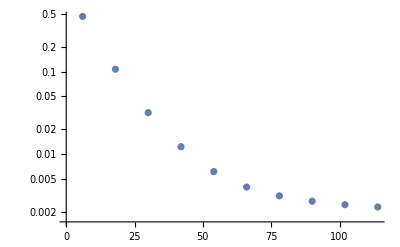

```mathematica
ListLogPlot[ratio]
```

```mathematica
(*the excitation of QNM is more prominent for lower values of the secondary radius*)
```

## OTHER MASSES

```mathematica
(*this analysis can be repeated for other values of the scalar field and black hole mass. We find here the eigenfrequencies of QBSs and QNMs*)
```

### α = 0.1

#### fundamental QBS 0.1

```mathematica
mu0=0.1;
a0=0.0;
l0=1;
m0=1;
N0=1000;
wguess=0.09761923463865892-9.455651630455782*^-6 ⅈ;

f[x_?NumberQ]:=INT[x,mu0,a0,l0,m0,0,N0, -1];
root=x/.FindRoot[f[x],{x,wguess}];
check=Abs[f[root]];
{root,check}
```

{0.0998736-1.33554×10^-11 ⅈ,6.52379×10^-11}

```mathematica
ωn1=0.09987363876896593-1.3355436171364277*^-11 ⅈ;
```

```mathematica
ae[0]=1;
ae[1]=-β[0]/α[0]/.w->root;
i=1;While[i<N0,ae[i+1]=(-β[i]*ae[i]-γ[i]*ae[i-1])/(α[i])/.w->root;i=i+1];
```

```mathematica
chi=(mu0^2-2*w^2)/q/.w->root;
sigma=2*rplus*(w-m0*a0/(2*M*rplus))/(rplus-rminus)/.w->root;
Rpsi=(Exp[I Pi/2](r-rplus))^(-I*sigma)Exp[(-I Pi/2)(-I sigma)]*(r-rminus)^(I*sigma+chi-1)*Exp[q*r]*Sum[ae[n]*(r-rplus)^n/(r-rminus)^n,{n,0,N0}];
```

General::munfl: 0.0504933^1000 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.05049^1000 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0504933^999 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

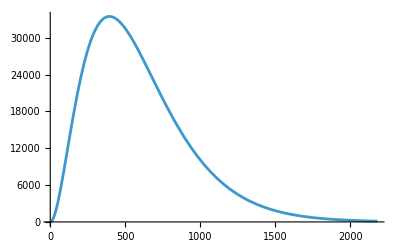

```mathematica
Plot[{Abs[Rpsi*r]},{r,2.006,2180}, PlotRange->All]
```

#### fundamental QNM 0.1

```mathematica
mu0=0.1;
a0=0;
l0=1;
m0=1;
N0=1000;
wguess=0.297- 0.094823 I;

f[x_?NumberQ]:=INT[x,mu0,a0,l0,m0,0,N0, 1];
root=x/.FindRoot[f[x],{x,wguess}];
check=Abs[f[root]];
{root,check}
```

{0.297416-0.0949571 ⅈ,4.77525×10^-16}

```mathematica
ωnQNM=0.29741566124545843-0.09495707360620889 ⅈ;
```

### α = 0.2

#### fundamental QBS 0.2

```mathematica
mu0=0.2;
a0=0.0;
l0=1;
m0=1;
N0=1000;
wguess=ωQBS[2,1,1];

f[x_?NumberQ]:=INT[x,mu0,a0,l0,m0,0,N0, -1];
root=x/.FindRoot[f[x],{x,wguess}];
check=Abs[f[root]];
{root,check}
```

{0.198953-4.06044×10^-8 ⅈ,1.13801×10^-12}

```mathematica
ωn1=0.19895266125256714-4.060438231863658*^-8 ⅈ;
```

#### fundamental QNM 0.2

```mathematica
mu0=0.2;
a0=0.0;
l0=1;
m0=1;
N0=1000;
wguess=0.310957- 0.086593 I;

f[x_?NumberQ]:=INT[x,mu0,a0,l0,m0,0,N0, 1];
root=x/.FindRoot[f[x],{x,wguess}];
check=Abs[f[root]];
{root,check}
```

{0.310957-0.0865933 ⅈ,2.83052×10^-16}

```mathematica
ωnQNM=0.3109569083982675-0.08659328561563795 ⅈ;
```